```mathematica
<<mf25.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];
Return[collect2]]
```

```mathematica
fLambda2[n_,m_]:=
Module[{jay,djay,numerator,denominator,answer},
jay=jNew[n+1,m]; (* n+1 instead of n avoids erros in highest order term. Why? *)
djay=x*D[jay,x];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-2^6*m^3);
answer=Collect[Series[(numerator/denominator)^(1/(m-2)),{x,0,n}],x];
Return[answer]]
```

```mathematica
fL=fLambda2[25,3];
Print[fL];
no=0;
For[n=0,n<25,n++;
cf=Coefficient[fL,x,n];
s3=DivisorSigma[3,n];
If[cf/240≠s3,no++]];
Print[no]
```

1+240 x+2160 x^2+6720 x^3+17520 x^4+30240 x^5+60480 x^6+82560 x^7+140400 x^8+181680 x^9+272160 x^10+319680 x^11+490560 x^12+527520 x^13+743040 x^14+846720 x^15+1123440 x^16+1179360 x^17+1635120 x^18+1646400 x^19+2207520 x^20+2311680 x^21+2877120 x^22+2920320 x^23+3931200 x^24+3780240 x^25

0

```mathematica
stream=OpenWrite["run29jun20no5"];
start=SessionTime[];
For[m=2,m<98,m++;
expansion=fLambda2[25,m];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 18.2206

```mathematica
stream=OpenWrite["run6sept20no1"];
start=SessionTime[];
For[m=2,m<302,m++;
expansion=fLambda2[101,m];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 9824.2161

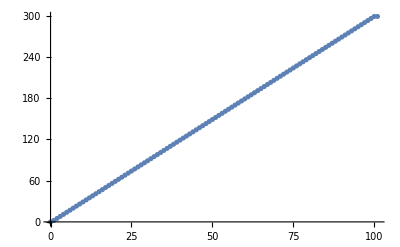

run6sept20no5

```mathematica
stream=OpenRead["run6sept20no1"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run6sept20no5"];
degrees={};
For[n=-1,n<101,n++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

#### Entry 102 is anomalous. (Insufficient data to interpolate.)

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

102

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
no={};
For[k=1,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
ex=Exponent[poly,x];
If[ex=!=3*n-1,AppendTo[no,k]]];
Print[no]
```

{102}

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
For[k=0,k<5,k++;
Print["***********************************************"];
index=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
poly=Factor[poly];
Print[{index,poly}]]
```

***********************************************

{0,1}

***********************************************

{1,16 x (2+x)}

***********************************************

{2,-16 (-6+x) (-2+x) x^2 (2+x)}

***********************************************

{3,64/9 (-2+x) x^3 (2+x) (-296+164 x-30 x^2+3 x^3)}

***********************************************

{4,-16/27 (-2+x) x^4 (2+x) (-99616+82480 x-28976 x^2+6152 x^3-738 x^4+27 x^5)}

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
For[k=2,k<5,k++;
Print["***********************************************"];
index=list[[k,1]];
poly=list[[k,2]];
denominator=(x^2-4)*x^index;
poly=poly/denominator;
poly=Collect[poly,x];
poly=Factor[poly];
poly=Expand[poly];
Print[{index,poly}]]
```

***********************************************

{2,96-16 x}

***********************************************

{3,-18944/9+(10496 x)/9-(640 x^2)/3+(64 x^3)/3}

***********************************************

{4,1593856/27-(1319680 x)/27+(463616 x^2)/27-(98432 x^3)/27+(1312 x^4)/3-16 x^5}

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

102

```mathematica
qlist={2,5,6,8,10,11,14,15,17,18,20,22,23,24,26,29,30,32,33,34,35,38,40,41,42,44,45,46,47,50,51,53,54,55,56,58,59,60,62,65,66,68,69,70,71,72,74,77,78,80,82,83,85,86,87,88,89,90,92,94,95,96,98,99}
```

{2,5,6,8,10,11,14,15,17,18,20,22,23,24,26,29,30,32,33,34,35,38,40,41,42,44,45,46,47,50,51,53,54,55,56,58,59,60,62,65,66,68,69,70,71,72,74,77,78,80,82,83,85,86,87,88,89,90,92,94,95,96,98,99}

#### Clause 1 of conjecture 4.

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<101,k++;
index=list[[k,1]];
poly=list[[k,2]];
poly=poly;
poly=Collect[poly,x];
poly=Factor[poly];
poly=Expand[poly];
If[PolynomialQ[poly,x]=!=True,AppendTo[data,{index,poly}]]];
Print[data]
```

{}

#### Second part of clause 4 of conjecture 4 (not the claim about e_n, but the rest of it.)

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
data={};
For[k=2,k<101,k++;
index=list[[k,1]];
If[MemberQ[qlist,index]===False,
poly=list[[k,2]];
denominator=(x^2-4)*x^(index);
poly=poly/denominator;
poly=Collect[poly,x];
poly=Factor[poly];
poly=Expand[poly];
If[IrreduciblePolynomialQ[poly]===False,AppendTo[data,index]]]];
Print[data]
```

{}

#### First part of clause 4 of conjecture 4 (not the claim about e_n, but the rest.)

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
data={};
For[k=2,k<101,k++;
index=list[[k,1]];
If[MemberQ[qlist,index]===True,
poly=list[[k,2]];
denominator=(x^2-4)*x^(index)*(x-6);
poly=poly/denominator;
poly=Collect[poly,x];
poly=Factor[poly];
poly=Expand[poly];
If[IrreduciblePolynomialQ[poly]===False,AppendTo[data,index]]]];
Print[data]
```

{2}

#### conjecture 4, clause 2:

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
For[k=0,k<101,k++;
index=list[[k,1]];
poly=list[[k,2]];
ex=Exponent[poly,x];
If[ex=!=3*index-1,Print[{index,poly}]]]
```

{0,1}

#### Conjecture 4, clause 4:

```mathematica
specialsum[n_]:=Module[{lnth,k,answer,d},
answer=0;
lnth=Length[Divisors[n]];
For[j=0,j<lnth,j++;
d=Divisors[n][[j]];
If[Mod[d,2]==1,answer=answer+1/d]];
Return[answer*16*(-1)^(n+1)]]
```

#### clause 4 conjecture 4: e_n claim.

```mathematica
stream=OpenRead["run6sept20no5"];
list=ReadList[stream];
Close[stream];
data={};
ntdata={};
For[k=0,k<100,k++;
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
numericalterm=1;
For[j=0,j<Length[fim],j++;
pair=fim[[j]];
base=pair[[1]];
power=pair[[2]];
dg=Exponent[base,x];
If[dg===0,
numericalterm=numericalterm*base^power]];
AppendTo[ntdata, specialsum[n]-numericalterm]];
Print[ntdata]
```

{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}